```mathematica
SetDirectory["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\danal\Documents\GitHub\Tesis-de-Licenciatura\Figuras

```mathematica
a3=2.6;
b3=2.7;
c3=2;
```

```mathematica
a=2.65;
b=2.75;
c=1;
```

1.77067

1.83467

1.36341/b21

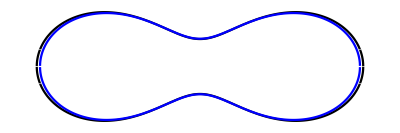

```mathematica
a=2.656;
b=2.752;
c=1;
a2=2.656/1.5
b2=2.752/1.5
a2/b21.77
z1[x_]:=c(-a^2-x^2+(4 x^2 a^2+b^4)^(1/2))^(1/2)
z11[x_]:=-c(-a^2-x^2+(4 x^2 a^2+b^4)^(1/2))^(1/2)

z2[x_]:=c(-a2^2-x^2+(4 x^2 a2^2+b2^4)^(1/2))^(1/2)
z22[x_]:=-c(-a2^2-x^2+(4 x^2 a2^2+b2^4)^(1/2))^(1/2)

z3[x_]:=c(-a3^2-x^2+(4 x^2 a3^2+b3^4)^(1/2))^(1/2)
z33[x_]:=-c(-a3^2-x^2+(4 x^2 a3^2+b3^4)^(1/2))^(1/2)
zT[x_]:=((1-(x/3.825)^2)^(0.5))*(0.72+4.152*(x/3.825)^2-3.426*(x/3.825)^4)
zT2[x_]:=-((1-(x/3.825)^2)^(0.5))*(0.72+4.152*(x/3.825)^2-3.426*(x/3.825)^4)
comparacionGeometrias=Plot[{Style[z1[x],Black],Style[z11[x],Black],Style[z3[x],Blue],Style[z33[x],Blue]},{x,-3.83,3.83},AspectRatio->1/3,Axes->False]
```

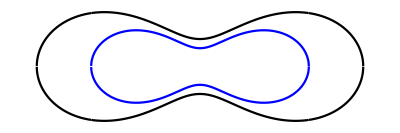

```mathematica
comparacionGeometrias=Plot[{Style[z1[x],Black],Style[z11[x],Black],Style[z2[x],Blue],Style[z22[x],Blue]},{x,-3.83,3.83},AspectRatio->1/3,Axes->False]
```

```mathematica
a/b
```

0.965116

0.965116

0.96641

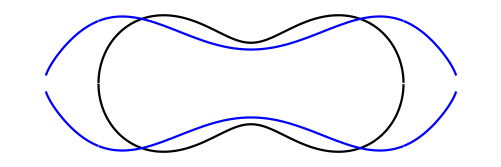

```mathematica
z[3]
```

```mathematica
Export["Geometrias.svg",comparacionGeometrias]
```

Geometrias.svg

NMinimize::lvar: Variables {2.656,2.752,1} should be a list of variables, with each element being a variable, or a list containing a variable and lower and upper bounds for the starting region for that variable.

NMinimize[{0.665238,{False,False,True,True,True}},{2.656,2.752,1}]

{2.656,2.752,1}

ReplaceAll::reps: {2.656,2.752,1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.656,2.752,1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2.656,2.752,1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

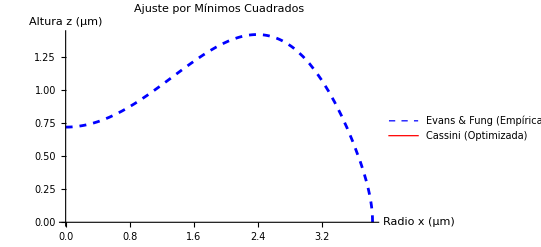

```mathematica
(*1. Definir la curva de referencia empírica (Evans& Fung)*)Rmax=3.825;
zEF[x_]:=Sqrt[1-(x/Rmax)^2]*(0.72+4.152*(x/Rmax)^2-3.426*(x/Rmax)^4)

(*2. Definir tu modelo paramétrico (Óvalo de Cassini)*)
zCas[x_,a_,b_,c_]:=c*Sqrt[-a^2-x^2+Sqrt[4*x^2*a^2+b^4]]

(*3. Crear la Función de Error (Suma de los Cuadrados de los Errores-SSE)*)
(*Comparamos la altura de ambas curvas cada 0.05 micras a lo largo del radio*)
funcionError=Sum[(zCas[x,a,b,c]-zEF[x])^2,{x,0,3.8,0.05}];

(*4. Definir las reglas biológicas inquebrantables (Restricciones)*)
restricciones={a^2+b^2==Rmax^2,(*Regla 1:El radio exterior debe ser exactamente 3.825*)c*Sqrt[b^2-a^2]==0.72,(*Regla 2:La profundidad central debe ser exactamente 0.72*)a>0,b>a,c>0          (*Regla 3:Físicamente debe ser un eritrocito bicóncavo real*)};

(*5. Ejecutar el algoritmo numérico para encontrar la solución única*)
solucion=NMinimize[{funcionError,restricciones},{a,b,c}]

(*6. Extraer los valores óptimos encontrados por Mathematica*)
valoresOptimos=solucion[[2]]

(*7. Graficar ambas curvas juntas para comprobar visualmente el ajuste*)
Plot[{zEF[x],zCas[x,a,b,c]/. valoresOptimos},{x,0,Rmax},PlotStyle->{{Dashed,Blue,Thickness[0.005]},{Red,Thickness[0.005]}},PlotLegends->{"Evans & Fung (Empírica)","Cassini (Optimizada)"},PlotRange->All,AxesLabel->{"Radio x (μm)","Altura z (μm)"},PlotLabel->"Ajuste por Mínimos Cuadrados"]
```